# Data from ContourPlot

```mathematica
M=1000000;
d=0.0005;

p[cp_,g_]:=Sqrt[(2*Pi*g*M/1716)^2-(2*Pi*g*M/(cp))^2];
q[cp_,g_]:=Sqrt[(2*Pi*g*M/785)^2-(2*Pi*g*M/(cp))^2];



sy[cp_,g_,p_,q_]:=(((2*Pi*g*M/(cp))^2-q^2)^2) Cos[p*d] Sin[q*d]+4 ((2*Pi*g*M/(cp))^2) p q Sin[p*d] Cos[q*d]
sy[cp_,g_]:=sy[cp,g,p[cp,g],q[cp,g]];

as[cp_,g_,p_,q_]:=(((2*Pi*g*M/(cp))^2-q^2)^2) Sin[p*d] Cos[q*d]+4 ((2*Pi*g*M/(cp))^2) p q Cos[p*d] Sin[q*d]
as[cp_,g_]:=as[cp,g,p[cp,g],q[cp,g]];

ContourPlot[{sy[cp,g]/q[cp,g]==0,as[cp,g]/p[cp,g]==0},{g,0.001,0.1},{cp,0.01,2000},PlotPoints->100]
```

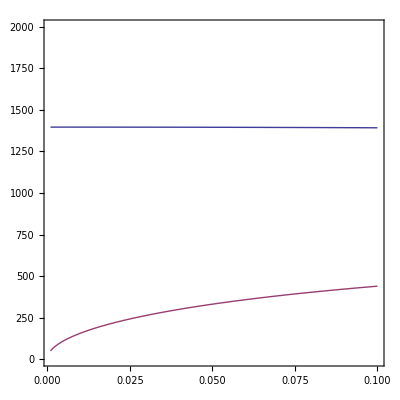
```mathematica
Clear@plot
plot=-Graphics-
```

```mathematica
{#⟦1,0⟧,#⟦1,1,0⟧}&@FullForm@plot
(*SetDirectory["/Users/chapman5/Desktop"]
Export["data.txt",%%]*)
```

```mathematica
FullForm@plot
Normal@%⟦1⟧//Short[#,1]&
pts=Cases[%,Line[pts_]:>pts,∞](*//Short[#,2]&*)
pts>>"data.m"
```

```mathematica
SetDirectory["/Users/chapman5/Desktop"];
ListPlot@<<"data.m"
```